```mathematica
StringReverse["hello"]
```

olleh

```mathematica
ToUpperCase[%]
```

OLLEH

```mathematica
StringTake[%,3]
```

OLL

```mathematica
Characters["a string made of characters"]
```

{a, ,s,t,r,i,n,g, ,m,a,d,e, ,o,f, ,c,h,a,r,a,c,t,e,r,s}

```mathematica
Sort[%]
```

{ , , , ,a,a,a,a,c,c,d,e,e,f,g,h,i,m,n,o,r,r,r,s,s,t,t}

```mathematica
TextWords["a string made of characters"]
```

{a,string,made,of,characters}

```mathematica
StringLength[%]
```

{1,6,4,2,10}

```mathematica
StringTake[WikipediaData["Chile"],100]
```

Chile ( (listen), ; Spanish: [ˈtʃile]), officially the Republic of Chile (Spanish: República de Chil

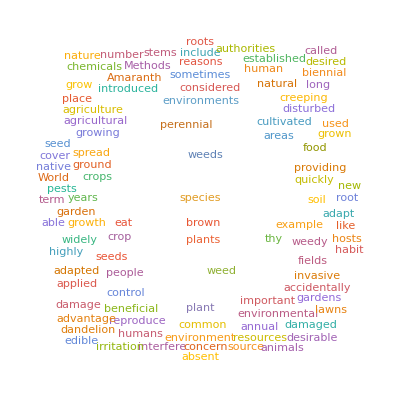

```mathematica
WordCloud[WikipediaData["Weed"]]
```

```mathematica
WordList[]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,40097,zone,zoning,zoo,zoological,zoologist,zoology,zoom,zoophyte,zounds,zucchini,zwieback,zydeco,zygote,zygotic,zymurgy}
 |  |  |  |

```mathematica
WordList[Language->"Spanish"]
```

{a,aarónica,aarónico,ab,abab,ababillarse,ababol,abacá,abacera,abacería,abacero,abacial,ábaco,abad,85988,zurruscarse,zurrusco,zurubí,zurugía,zurujano,zurullo,zurumbática,zurumbático,zurupeto,zutana,zutano,zuzar,zuzo,zuzón}
 |  |  |  |

```mathematica
BarChart[StringTake[%,1]]
```

$Aborted

```mathematica
RomanNumeral[1999]
```

MCMXCIX

```mathematica
Table[RomanNumeral[n],{n,20}]
```

{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX}

```mathematica
Column[{"I","II","III","IV","V","VI","VII","VIII","IX","X","XI","XII","XIII","XIV","XV","XVI","XVII","XVIII","XIX","XX"}]
```

I
II
III
IV
V
VI
VII
VIII
IX
X
XI
XII
XIII
XIV
XV
XVI
XVII
XVIII
XIX
XX

```mathematica
ListLinePlot[Table[StringLength[RomanNunerak[n]],{n,30}]]
```

StringLength::string: String expected at position 1 in StringLength[RomanNunerak[1]].

StringLength::string: String expected at position 1 in StringLength[RomanNunerak[2]].

StringLength::string: String expected at position 1 in StringLength[RomanNunerak[3]].

General::stop: Further output of StringLength::string will be suppressed during this calculation.

-Graphics-

```mathematica
Table[StringLength[RomanNumeral[n]],{n,30}]
```

{1,2,3,2,1,2,3,4,2,1,2,3,4,3,2,3,4,5,3,2,3,4,5,4,3,4,5,6,4,3}

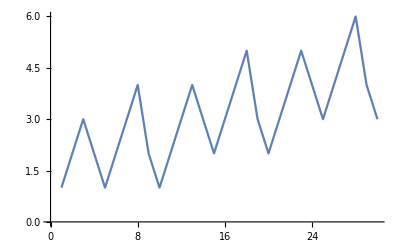

```mathematica
ListLinePlot[%]
```

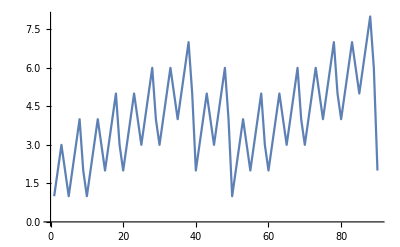

```mathematica
ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,90}]]
```

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Alphabet[Language->"Spanish"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
LetterNumber[{"a","b","c","e","z"}]
```

{1,2,3,5,26}

```mathematica
Transliterate[Alphabet["Russian"]]
```

{a,b,v,g,d,e,e,z,z,i,j,k,l,m,n,o,p,r,s,t,u,f,h,c,c,s,s,",y,',e,u,a}

```mathematica
Transliterate[Alphabet["Romanian"]]
```

{a,a,a,b,c,d,e,f,g,h,i,i,j,k,l,m,n,o,p,q,r,s,s,t,t,u,v,w,x,y,z}

```mathematica
Alphabet["Romanian"]
```

{a,ă,â,b,c,d,e,f,g,h,i,î,j,k,l,m,n,o,p,q,r,s,ș,t,ț,u,v,w,x,y,z}

```mathematica
Transliterate["Fabian","Russian"]
```

Фабиан

```mathematica
Rasterize[%]
```

-Graphics-

```mathematica
EdgeDetect[%]
```

-Graphics-

```mathematica
Style[%,100]
```

-Graphics-

```mathematica
EdgeDetect[Blur[Rasterize[Style[Transliterate["Fabian","Russian"],100]]]]
```

-Graphics-

```mathematica
(*11.4*)
```

```mathematica
StringJoin@Table["AGCT",{n,100}]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
(*11.5*)
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
Column@Table[StringTake["this is about strings",n],{n,StringLength["this is about strings"]}]
```

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

```mathematica
StringLength[WikipediaData["computer"]]
```

52079

```mathematica
WordCount[WikipediaData["computer"]]
```

8046

```mathematica
Max[StringLength@WordList[]]
```

23

```mathematica
(*Cuantas Palabras del alfabeto ingles empiezan con q*)
```

```mathematica
StringTake[WordList[],1] (*Entrega la primera letra de cada palabra*)
Count[list,pattern] (*Entrega el numero de veces que aparece el elemnto*)
```

```mathematica
(*Asi que para el ejercicio*)
Count[StringTake[WordList[],1],"q"]
```

```mathematica
197 (*Lo cual es correcto!!*)
```

```mathematica
(*Mayor longitud de cadena entre los a;os 1 al 2020 en romano*)
Table[RomanNumeral[n],{n,2020}] (*Entrega una lista de los numeros en romano hasta el 2020*)

Max@StringLength[] (*Valor maximo de las longitudes de cadena*)
```

```mathematica
(*Ahora la respuesta*)
Max@StringLength@Table[RomanNumeral[n],{n,2020}]
```

```mathematica
13(*Correcto!!*)
```